```mathematica
SetDirectory[NotebookDirectory[]]
data=Import["PMdata.csv"];
dataNewton = Import["newtondata.csv"];
{x1,y1,z1,px1,py1,pz1,x2,y2,z2,px2,py2,pz2,x3,y3,z3,px3,py3,pz3,hamil}=data;
{x12,y12,z12,px12,py12,pz12,x22,y22,z22,px22,py22,pz22,x32,y32,z32,px32,py32,pz32,hamil2}=dataNewton;
```

/Users/zackarywindham/Research/Post-Minkowski/julia_code

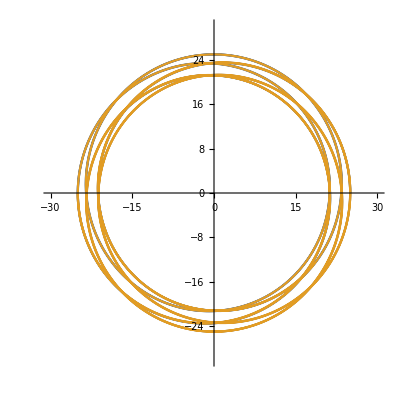

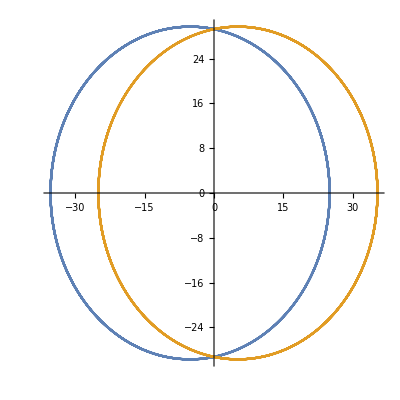

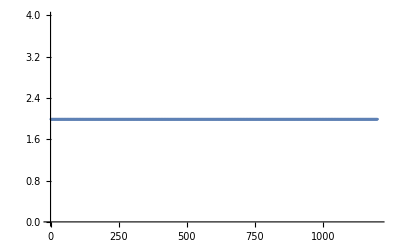

```mathematica
ListPlot[{Transpose[{x1,y1}],Transpose[{x2,y2}](*,Transpose[{x3,y3}]*)},AspectRatio->1,Joined->True,PlotRange->{{-30,30},{-30,30}}]
ListPlot[{Transpose[{x12,y12}],Transpose[{x22,y22}](*,Transpose[{x32,y32}]*)},AspectRatio->1,Joined->True]
ListPlot[Delete[hamil,1]]
```